```mathematica
Quit[];
```

```mathematica
(*diseased state*)
Wss=0;
Wgs=10.7;
Wsg=20;
Wgg=12.3;
Wcs=9.2;
Wxg=139.4;
Ctx=27;
Str=2;
Ms = 300;
Mg = 400;
Bs = 17;
Bg = 75;
tauS=6 (*assume tau_s=tau_g*);
```

```mathematica
(* Rescaled System's coefficients and function definition *)
ac=Wss;
bc=-Wgs;
cc=Wsg;
dc=-Wgg;
tu=Wcs*Ctx;
tv=-Wxg*Str;
f1[in1_]:=Ms/(1+Exp[-4*in1/Ms]*(Ms-Bs)/Bs);
f2[in2_]:=Mg/(1+Exp[-4*in2/Mg]*(Mg-Bg)/Bg);
F[u_,ud_]:={
-u[[1]]+f1[tu+ac*ud[[1]]+bc*ud[[2]]],
-u[[2]]+f2[tv+cc*ud[[1]]+dc*ud[[2]]]}
```

```mathematica
(*equilibrium point*)
eq={u,v}/.FindRoot[F[{u,v},{u,v}]=={0,0},{{u,0},{v,0}}]
```

{20.4425,21.8366}

```mathematica
(*characteristic parameter values*)
alpha=ac*f1'[tu+ac*eq[[1]]+bc*eq[[2]]]+dc*f2'[tv+cc*eq[[1]]+dc*eq[[2]]]
beta=(ac*dc-bc*cc)*f1'[tu+ac*eq[[1]]+bc*eq[[2]]]*f2'[tv+cc*eq[[1]]+dc*eq[[2]]]
```

-2.53928

11.2213

```mathematica
(*Strong Gamma kernel - Laplace transform and related functions defined in paper*)
H[z_]:=1/(1+z);
Q[t_,z_]:=(z+t)/(t*H[z]);
al[t_,w_]:=2-(2 w^2)/t;(*given explicitely for ease of computation*)
be[t_,w_]:=1+w^2+w^2/t^2+w^4/t^2;(*given explicitely for ease of computation*)
Co[t_,w_]:=Re[H[I*w]];
rho[w_]:=1/Sqrt[1+w^2]; (*given explicitely for ease of computation*)
theta[w_]:=ArcTan[w]; (*given explicitely for ease of computation*)
```

```mathematica
(*values of tau and corresponding frequency such that (alpha,beta) is on the curve (gamma_tau) *)
NSolve[{alpha==al[t,w],beta==be[t,w],t>0,w>0},{t,w},Reals]
```

{{t→0.619418,w→1.18569},{t→1.61442,w→1.9142}}

```mathematica
(*Use Theorem 2.9 to detect critical value of time delay and frequency - along the curve (gamma_tau)*)
{Tau,W}={t,w}/.NSolve[{alpha==al[t,w],beta==be[t,w],t>0,w>0},{t,w},Reals][[1]]
```

{0.619418,1.18569}

```mathematica
(*There is a second critical value of the time delay where stability is regained *)
{Tau2,W2}={t,w}/.NSolve[{alpha==al[t,w],beta==be[t,w],t>0,w>0},{t,w},Reals][[2]]
```

{1.61442,1.9142}

```mathematica
(*predicted frequency of oscillations at first Hopf bifurcation - divided by Tau due to relation between \Delta and \hat{\Delta}*)
freq=W/(Tau*2*Pi)
```

0.304654

```mathematica
(*frequency of oscillations at Hopf bifurcation - rescaled*)
freq/(tauS*10^(-3))
```

50.7756

```mathematica
(*stability region for Strong Gamma kernel, together with point of coordinates (alpha, beta) - uses range accoring to bifurcation values, so that domains can be compared - using inequalities in Example 2.2*)
pw[t_]:=
Show[RegionPlot[x-1<y<(1-x/2)^2+(t+1/t)*(1-x/2)+1&&x<2,{x,-10,2},{y,-12,20},PlotPoints->100],
Plot[x-1,{x,-10,2},PlotStyle->Red],
Graphics[{Red,PointSize[0.04],Point[{alpha,beta}]}],
LabelStyle->Directive[Bold,Black, FontSize->20],ImageSize->{Automatic,300},
Epilog->Inset[Framed[Style[Row[{"W. Gamma, τ=",t}],Bold,19],Background->LightYellow,RoundingRadius->4],{-1,15}],
PlotRange->{{-4,2},{-5,17}}]
```

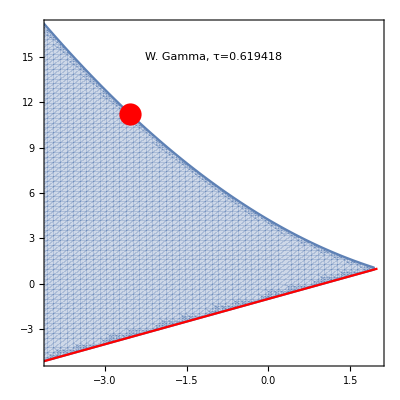

```mathematica
pw[Tau]
```

```mathematica
(*system with WEAK GAMMA kernel - using linear chain trick*)
sys[tau_]:={u'[t]==F[{u[t],v[t]},{ud1[t],vd1[t]}][[1]],
v'[t]==F[{u[t],v[t]},{ud1[t],vd1[t]}][[2]],
ud1'[t]==(u[t]-ud1[t])/tau,
vd1'[t]==(v[t]-vd1[t])/tau,
u[0]==0,
v[0]==0,
ud1[0]==0,
vd1[0]==0};
```

```mathematica
(*frequency at Hopf bifurcation computed based on the numerically evaluated solution - agrees with theoretically calculated value*)
Tmax=1000;
pts[tau_]:=Reap[s=NDSolve[{u'[t]==F[{u[t],v[t]},{ud1[t],vd1[t]}][[1]],
v'[t]==F[{u[t],v[t]},{ud1[t],vd1[t]}][[2]],
ud1'[t]==(u[t]-ud1[t])/tau,
vd1'[t]==(v[t]-vd1[t])/tau,
u[0]==eq[[1]]*1.1,
v[0]==eq[[2]]*1.1,
ud1[0]==eq[[1]]*1.1,
vd1[0]==eq[[2]]*1.1,
WhenEvent[v'[t]==0,Sow[t]]},{v,v'},{t,0.8*Tmax,Tmax}]][[2,1]];
frequency[tau_]:=1/Mean[Differences[pts[tau],1,2]]
```

```mathematica
(*frequency comupter numerically at bifurcation - rescaled - in Hz*)
frequency[Tau]/(tauS*10^(-3))
```

50.7343

```mathematica
pfreqWeak=Table[{del,frequency[del]/(tauS*10^(-3))},{del,Tau,Tau2,0.05}];
```

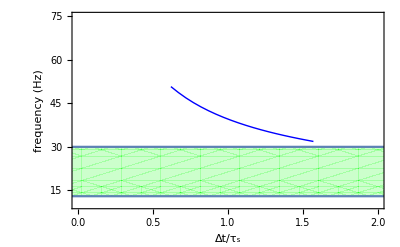

```mathematica
Show[ListPlot[pfreqWeak,Joined->True,PlotRange->All,PlotStyle->{Thick,Blue}],
RegionPlot[13<y<30,{x,-0.5,4.5},{y,10,90},PlotStyle->{Green,Opacity[0.2]}],
FrameLabel->{"Δt/τ_s","frequency (Hz)"},Frame->True,Axes->False,PlotRange->{{0,2},{10,75}}]
```

```mathematica
(*plot evolution of state variables*)
trans=0;Tmax=180/1.2;
p1[tau_]:=Plot[Evaluate[{u[(t+trans)/(tauS*10^(-3))],v[(t+trans)/(tauS*10^(-3))]} /. NDSolve[sys[tau],{u,v,ud1,vd1},{t,Tmax}]],{t,0,(Tmax-trans)*tauS*10^(-3)},PlotRange->All,Axes->False,Frame->True, PlotStyle->{{Thick,Red},{Thick,Blue}},FrameLabel->{None,"STN, GP vs. time (s)"},ImageSize->{Automatic,300},LabelStyle->Directive[Bold,Black, FontSize->20]]
```

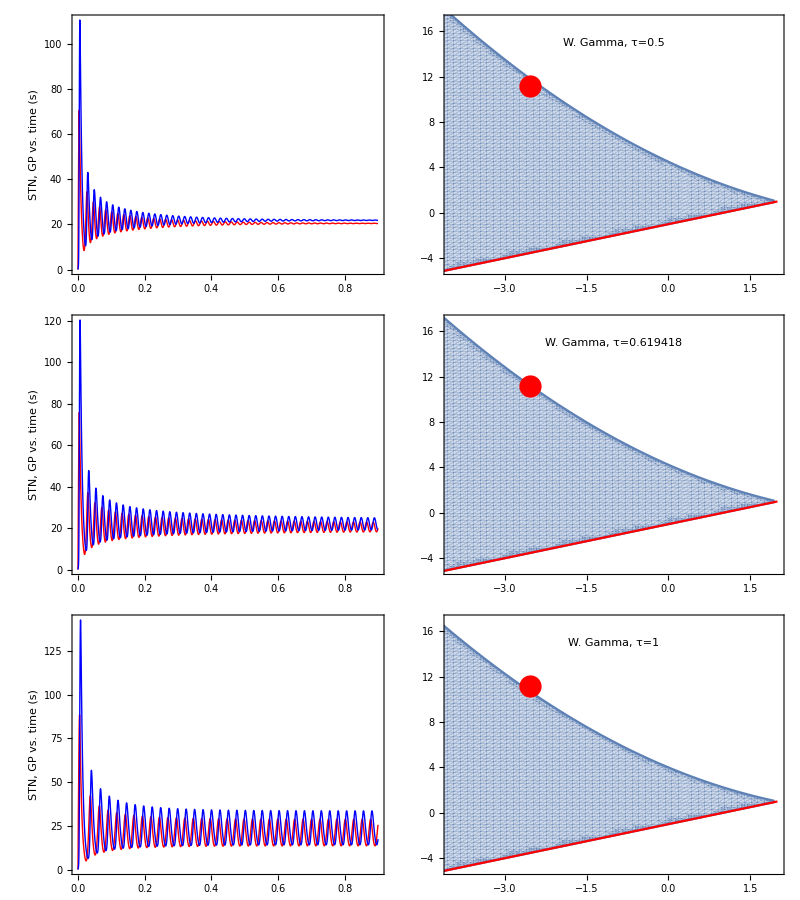

```mathematica
(*Graphics: evolution of state variables vs. stability domain*)
Grid[{{p1[0.5],pw[0.5]},{p1[Tau],pw[Tau]},{p1[1],pw[1]}}]
```

```mathematica
Tmax = 100;
trans=0;
p2[tau_]:=ParametricPlot[Evaluate[{u[(t+trans)],v[(t+trans)]} /. NDSolve[sys[tau],{u,v,ud,vd},{t,Tmax}]],{t,0,Tmax-trans},Axes->False,Frame->True,AspectRatio->1,PlotRange->All,PlotLabel->Row[Style[#,14] & /@{"τ=",tau}],LabelStyle->Directive[Bold,Black, Larger], (*ColorFunction->{Red, Blue}*) ColorFunction->(ColorData[{"LightTemperatureMap","Reversed"}][#3]&), ImageSize->{Automatic,300},FrameStyle->Directive[FontSize->14]]
```

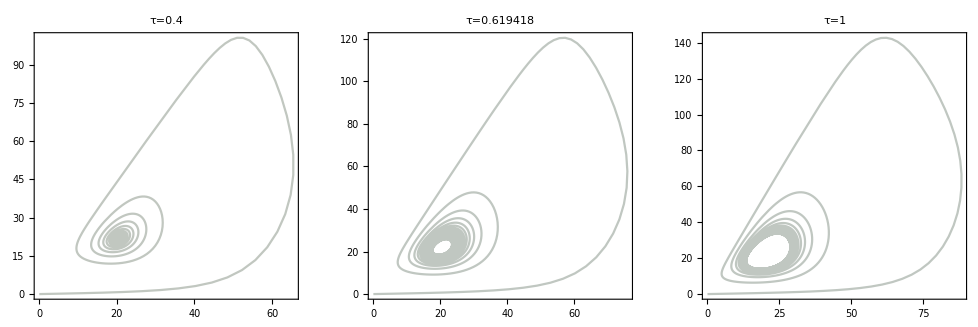

```mathematica
Show[GraphicsGrid[{{p2[0.4],p2[0.619418], p2[1]}}]]
```